```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eric/git/nonlinear-systems-lab/Project 1

```mathematica
rawdata=Import["data/raw/rocking1.tsv"]
```

{{time,1,2,3,4},{153.815,300,300,158.25,},{153.815,300,300,,601.5},{153.845,300,300,157.75,},{153.845,300,300,,600.75},1542,{177.536,300,300,,549.25},{177.58,300,300,105.75,},{177.58,300,300,,549.25},{177.609,300,300,105.75,},{177.609,300,300,,549.25}}
 |  |  |  |

```mathematica
tagDist=.396;
pivotFromTag =tagDist*0.26582;
pendulumlen = 0.335;
```

# Unify timestamps

```mathematica
preprocess[rawdata_]:=Module[{(*header,gathered,data,meandist, x,x1,x2,θ1,θ2*)},
header=ToString/@rawdata[[1]];
gathered=Gather[rawdata[[2;;All]],First[#1]==First[#2]&];
data=Transpose[Mean[Select[#,NumberQ]]&/@Transpose[#]&/@gathered];
meandist = Mean[Select[data[[5]]-data[[4]],NumberQ]];
(*Print[meandist];*)

(* Convert to meters *)
data[[2;;All]]= data[[2;;All]]*tagDist/meandist;

x=Mean[{data[[4]],data[[5]]-tagDist}];

x1=data[[3]]-(x+pivotFromTag);
x2=data[[2]]-(x+tagDist-pivotFromTag+.003);

θ1=ArcSin[x1/pendulumlen];
θ2=ArcSin[x2/pendulumlen];

Prepend[
Cases[
Transpose@{data[[1]],x,θ1,θ2},{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}],{"Time", "x", "theta1", "theta2"}]
]
```

```mathematica
ListLinePlot[{x,x1,x2}]
```

-Graphics-

```mathematica
data=preprocess[rawdata]
```

{{Time,x,theta1,theta2},{153.815,0.14123,0.063944,-0.522096},{153.845,0.140671,0.0656136,-0.520175},{153.879,0.139555,0.0689533,-0.516339},{153.924,0.138439,0.0722937,-0.512512},{153.949,0.137155,0.0761362,-0.50812},{153.979,0.135983,0.0796455,-0.50412},{154.012,0.134644,0.0836574,-0.499559},{154.047,0.133081,0.0883397,-0.494253},{154.08,0.13163,0.0926892,-0.489339},{154.114,0.130179,0.0970405,-0.484437},{154.15,0.128393,0.102398,-0.478422},{154.184,0.126718,0.107424,-0.4728},{154.217,0.125044,0.112453,-0.467194},{154.248,0.123258,0.11782,-0.461232},{154.278,0.12136,0.123526,-0.454916},{154.314,0.119574,0.1289,-0.44899},{154.345,0.1179,0.133942,-0.443449},{154.378,0.116449,0.138314,-0.438659},{154.421,0.114886,0.143025,-0.433512},{154.454,0.113323,0.14774,-0.428378},{154.487,0.111426,0.153469,-0.422159},{154.513,0.109863,0.158191,-0.417051},{154.547,0.107854,0.164268,-0.410501},{154.58,0.106179,0.169337,-0.405056},{154.612,0.104393,0.174748,-0.399262},{154.657,0.102496,0.180503,-0.393122},{154.687,0.100486,0.186603,-0.386638},{154.73,0.0982538,0.19339,-0.379453},{154.755,0.0963561,0.199165,-0.373362},{154.786,0.0944585,0.204947,-0.367285},{154.817,0.0926725,0.210396,-0.361579},{154.85,0.0908865,0.21585,-0.355885},{154.88,0.0889889,0.221653,-0.349849},{154.913,0.0870912,0.227464,-0.343826},{154.946,0.0854168,0.232597,-0.338522},{154.99,0.0838541,0.237394,-0.33358},{155.023,0.0819565,0.243226,-0.327592},{155.053,0.0802821,0.248379,-0.322317},{155.084,0.078831,0.252851,-0.317754},{155.115,0.0773798,0.257327,-0.313197},{155.146,0.0756496,0.262672,-0.307773},{155.177,0.0740311,0.267678,-0.302708},{155.221,0.0728032,0.271481,-0.29887},{155.246,0.0712404,0.276326,-0.293992},{155.288,0.0699567,0.280312,-0.289991},{155.322,0.0685614,0.284649,-0.285647},{155.353,0.0673335,0.28847,-0.281829},{155.381,0.0661057,0.292295,-0.278015},{155.413,0.0648778,0.296125,-0.274206},{155.444,0.0637615,0.299611,-0.270746},{155.474,0.0629801,0.302053,-0.268326},{155.51,0.0616965,0.306069,-0.264354},{155.54,0.0608593,0.308691,-0.261766},{155.571,0.0601895,0.31079,-0.259697},{155.601,0.0596314,0.312541,-0.257973},{155.637,0.0591291,0.314117,-0.256423},{155.666,0.0591291,0.314117,-0.256423},{155.703,0.0586268,0.315694,-0.254873},{155.73,0.0586268,0.315694,-0.254873},{155.77,0.0583477,0.31657,-0.254012},{155.804,0.0586268,0.315694,-0.254873},{155.838,0.05885,0.314993,-0.255562},{155.87,0.05885,0.314993,-0.255562},{155.908,0.0592965,0.313591,-0.25694},{155.938,0.0596314,0.312541,-0.257973},{155.973,0.0604128,0.31009,-0.260387},{156.004,0.0608593,0.308691,-0.261766},{156.038,0.0617523,0.305894,-0.264527},{156.07,0.0625336,0.303449,-0.266944},{156.104,0.0639848,0.298913,-0.271438},{156.137,0.0648778,0.296125,-0.274206},{156.17,0.0657708,0.293339,-0.276976},{156.196,0.0657708,0.293339,-0.276976},{156.224,0.0671103,0.289165,-0.281135},{156.257,0.0684498,0.284996,-0.2853},{156.29,0.0693428,0.282219,-0.288079},{156.319,0.0706823,0.278059,-0.292252},{156.352,0.0720218,0.273903,-0.29643},{156.388,0.0730264,0.270789,-0.299567},{156.423,0.0747008,0.265606,-0.304803},{156.454,0.0758171,0.262154,-0.308298},{156.479,0.0770449,0.258361,-0.312147},{156.511,0.0783844,0.254227,-0.316351},{156.554,0.0793891,0.25113,-0.319508},{156.579,0.0809518,0.246317,-0.324426},{156.61,0.0820681,0.242883,-0.327944},{156.654,0.0837425,0.237737,-0.333228},{156.687,0.0853052,0.23294,-0.338169},{156.72,0.0866447,0.228832,-0.34241},{156.754,0.0882075,0.224045,-0.347367},{156.789,0.0897702,0.219263,-0.352333},{156.818,0.0911656,0.214998,-0.356774},{156.858,0.0924492,0.211077,-0.360867},{156.891,0.0939004,0.206649,-0.365501},{156.924,0.0954631,0.201885,-0.370501},{156.956,0.0969143,0.197466,-0.375152},{156.993,0.0985886,0.192371,-0.380529},{157.026,0.0999281,0.188299,-0.38484},{157.056,0.101491,0.183552,-0.389878},{157.089,0.10283,0.179487,-0.394205},{157.122,0.104282,0.175086,-0.398901},{157.154,0.105621,0.171027,-0.403244},{157.181,0.106849,0.167309,-0.407232},{157.215,0.108077,0.163593,-0.411228},{157.243,0.109416,0.159541,-0.415594},{157.273,0.110533,0.156167,-0.419239},{157.304,0.111202,0.154144,-0.421429},{157.338,0.111202,0.154144,-0.421429},{157.371,0.1131,0.148414,-0.427645},{157.402,0.113881,0.146056,-0.43021},{157.439,0.114886,0.143025,-0.433512},{157.465,0.114886,0.143025,-0.433512},{157.496,0.115444,0.141342,-0.435349},{157.526,0.116449,0.138314,-0.438659},{157.558,0.116784,0.137305,-0.439763},{157.59,0.117788,0.134278,-0.44308},{157.624,0.118458,0.132261,-0.445294},{157.654,0.119239,0.129908,-0.44788},{157.685,0.119797,0.128228,-0.449729},{157.717,0.120579,0.125876,-0.452321},{157.747,0.121249,0.123862,-0.454545},{157.78,0.121918,0.121847,-0.456771},{157.819,0.122811,0.119162,-0.459744},{157.846,0.123704,0.116478,-0.462721},{157.878,0.124374,0.114465,-0.464956},{157.912,0.1251,0.112285,-0.467381},{157.946,0.125825,0.110106,-0.469808},{157.987,0.12683,0.107089,-0.473174},{158.02,0.1275,0.105079,-0.475422},{158.052,0.128169,0.103068,-0.477672},{158.087,0.128727,0.101394,-0.479549},{158.12,0.129174,0.100054,-0.481051},{158.153,0.129732,0.0983797,-0.482932},{158.18,0.130067,0.0973753,-0.484061},{158.219,0.130234,0.0968731,-0.484625},{158.244,0.130625,0.0957015,-0.485944},{158.286,0.13096,0.0946973,-0.487075},{158.319,0.131407,0.0933585,-0.488584},{158.354,0.131853,0.0920199,-0.490094},{158.386,0.131909,0.0918526,-0.490283},{158.419,0.131853,0.0920199,-0.490094},{158.444,0.131965,0.0916853,-0.490471},{158.475,0.132076,0.0913507,-0.490849},{158.505,0.131853,0.0920199,-0.490094},{158.538,0.131853,0.0920199,-0.490094},{158.57,0.13163,0.0926892,-0.489339},{158.598,0.13163,0.0926892,-0.489339},{158.635,0.131407,0.0933585,-0.488584},{158.681,0.131072,0.0943626,-0.487452},{158.706,0.13029,0.0967057,-0.484814},{158.739,0.129955,0.0977101,-0.483684},{158.772,0.129732,0.0983797,-0.482932},{158.803,0.129397,0.0993843,-0.481803},{158.836,0.128839,0.101059,-0.479924},{158.864,0.128839,0.101059,-0.479924},{158.894,0.128281,0.102733,-0.478047},{158.927,0.127946,0.103738,-0.476921},{158.958,0.127388,0.105414,-0.475047},{158.988,0.126718,0.107424,-0.4728},{159.019,0.125825,0.110106,-0.469808},{159.051,0.125267,0.111782,-0.467941},{159.085,0.124486,0.11413,-0.465329},{159.123,0.123816,0.116142,-0.463093},{159.158,0.123035,0.118491,-0.460488},{159.187,0.122476,0.120169,-0.458629},{159.223,0.12203,0.121511,-0.457143},{159.249,0.121249,0.123862,-0.454545},{159.312,0.120244,0.126884,-0.45121},{159.345,0.120021,0.127556,-0.45047},{159.378,0.119574,0.1289,-0.44899},{159.408,0.119351,0.129572,-0.44825},{159.439,0.118904,0.130916,-0.446772},{159.486,0.118793,0.131252,-0.446402},{159.512,0.118346,0.132597,-0.444925},{159.553,0.117788,0.134278,-0.44308},{159.58,0.117677,0.134614,-0.442711},{159.619,0.117007,0.136632,-0.4405},{159.642,0.116895,0.136968,-0.440131},{159.677,0.116225,0.138987,-0.437923},{159.709,0.115556,0.141006,-0.435716},{159.753,0.115221,0.142015,-0.434614},{159.787,0.114886,0.143025,-0.433512},{159.819,0.114105,0.145382,-0.430943},{159.852,0.113658,0.146729,-0.429477},{159.886,0.113212,0.148077,-0.428011},{159.919,0.112765,0.149424,-0.426547},{159.952,0.112319,0.150772,-0.425083},{159.981,0.111649,0.152795,-0.42289},{160.01,0.111426,0.153469,-0.422159},{160.043,0.110644,0.15583,-0.419604},{160.089,0.109919,0.158023,-0.417233},{160.109,0.109249,0.160048,-0.415048},{160.141,0.108579,0.162073,-0.412864},{160.172,0.10763,0.164944,-0.409774},{160.204,0.106626,0.167985,-0.406507},{160.236,0.105286,0.172042,-0.402157},{160.269,0.105286,0.172042,-0.402157},{160.305,0.103277,0.178132,-0.395649},{160.335,0.102272,0.18118,-0.392401},{160.363,0.102272,0.18118,-0.392401},{160.403,0.0998723,0.188469,-0.38466},{160.436,0.0998723,0.188469,-0.38466},{160.473,0.097584,0.195427,-0.377301},{160.511,0.0962445,0.199505,-0.373004},{160.554,0.0951283,0.202906,-0.369428},{160.577,0.0943469,0.205288,-0.366928},{160.609,0.0930074,0.209374,-0.362648},{160.639,0.0918911,0.212781,-0.359087},{160.673,0.0911097,0.215168,-0.356597},{160.707,0.0901051,0.218239,-0.353398},{160.738,0.0892679,0.220799,-0.350736},{160.785,0.0883191,0.223703,-0.347722},{160.819,0.0874261,0.226438,-0.344888},{160.844,0.0864773,0.229345,-0.34188},{160.884,0.0855285,0.232255,-0.338875},{160.92,0.0847471,0.234652,-0.336403},{160.952,0.0839657,0.237051,-0.333933},{160.978,0.0831843,0.239451,-0.331465},{161.01,0.0825146,0.24151,-0.329352},{161.052,0.0819565,0.243226,-0.327592},{161.084,0.0816216,0.244256,-0.326536},{161.111,0.0810635,0.245974,-0.324778},{161.142,0.0809518,0.246317,-0.324426},{161.173,0.0807286,0.247004,-0.323723},{161.206,0.0805053,0.247692,-0.32302},{161.239,0.0803937,0.248035,-0.322669},{161.269,0.0803937,0.248035,-0.322669},{161.301,0.0803937,0.248035,-0.322669},{161.332,0.0803937,0.248035,-0.322669},{161.362,0.080617,0.247348,-0.323372},{161.392,0.0808402,0.246661,-0.324074},{161.423,0.080896,0.246489,-0.32425},{161.459,0.0813983,0.244943,-0.325833},{161.492,0.0818448,0.243569,-0.32724},{161.521,0.0827378,0.240824,-0.330056},{161.555,0.0831843,0.239451,-0.331465},{161.586,0.0836308,0.23808,-0.332875},{161.617,0.0846355,0.234995,-0.33605},{161.651,0.0851936,0.233282,-0.337815},{161.683,0.0856401,0.231912,-0.339228},{161.72,0.0864215,0.229516,-0.341703},{161.752,0.0873145,0.22678,-0.344534},{161.786,0.0879842,0.224728,-0.346659},{161.812,0.0885424,0.22302,-0.348431},{161.848,0.089547,0.219946,-0.351623},{161.882,0.0899935,0.21858,-0.353043},{161.917,0.0908865,0.21585,-0.355885},{161.953,0.0918911,0.212781,-0.359087},{161.985,0.0926725,0.210396,-0.361579},{162.012,0.0935655,0.207671,-0.364431},{162.051,0.0942353,0.205628,-0.366571},{162.077,0.0952399,0.202566,-0.369786},{162.108,0.0960213,0.200185,-0.372289},{162.153,0.0969143,0.197466,-0.375152},{162.175,0.0974724,0.195767,-0.376943},{162.205,0.0980305,0.194069,-0.378736},{162.237,0.0989235,0.191353,-0.381606},{162.27,0.0998165,0.188638,-0.38448},{162.307,0.10071,0.185925,-0.387357},{162.342,0.101547,0.183383,-0.390058},{162.378,0.102161,0.181519,-0.39204},{162.411,0.102942,0.179148,-0.394566},{162.441,0.103444,0.177625,-0.39619},{162.474,0.10417,0.175425,-0.398539},{162.505,0.10484,0.173395,-0.400709},{162.538,0.105063,0.172718,-0.401433},{162.569,0.105733,0.170689,-0.403606},{162.601,0.106068,0.169675,-0.404693},{162.633,0.106068,0.169675,-0.404693},{162.664,0.106626,0.167985,-0.406507},{162.7,0.107072,0.166633,-0.407958},{162.73,0.107072,0.166633,-0.407958},{162.762,0.107463,0.16545,-0.409229},{162.802,0.107519,0.165281,-0.409411},{162.838,0.107519,0.165281,-0.409411},{162.869,0.107407,0.165619,-0.409047},{162.907,0.107072,0.166633,-0.407958},{162.935,0.107072,0.166633,-0.407958},{162.963,0.106737,0.167647,-0.406869},{162.994,0.106291,0.168999,-0.405419},{163.027,0.106068,0.169675,-0.404693},{163.059,0.105621,0.171027,-0.403244},{163.101,0.104951,0.173056,-0.401071},{163.134,0.104951,0.173056,-0.401071},{163.168,0.1035,0.177455,-0.396371},{163.193,0.1035,0.177455,-0.396371},{163.222,0.103277,0.178132,-0.395649},{163.26,0.102607,0.180164,-0.393483},{163.284,0.102105,0.181689,-0.39186},{163.315,0.101491,0.183552,-0.389878},{163.349,0.10071,0.185925,-0.387357},{163.384,0.100263,0.187281,-0.385918},{163.409,0.0995375,0.189486,-0.383582},{163.451,0.0989235,0.191353,-0.381606},{163.485,0.0985886,0.192371,-0.380529},{163.518,0.0979189,0.194408,-0.378377},{163.551,0.0971375,0.196786,-0.375868},{163.578,0.0964678,0.198825,-0.37372},{163.618,0.0959096,0.200525,-0.371931},{163.643,0.0953515,0.202225,-0.370143},{163.684,0.0945143,0.204777,-0.367464},{163.707,0.094012,0.206309,-0.365858},{163.742,0.0935655,0.207671,-0.364431},{163.774,0.093119,0.209033,-0.363005},{163.805,0.0926725,0.210396,-0.361579},{163.841,0.0925609,0.210736,-0.361223},{163.875,0.0918911,0.212781,-0.359087},{163.918,0.0916679,0.213463,-0.358375},{163.948,0.091333,0.214486,-0.357308},{163.98,0.0908307,0.216021,-0.355708},{164.018,0.0907749,0.216192,-0.35553},{164.051,0.0906632,0.216533,-0.355175},{164.076,0.0905516,0.216874,-0.354819},{164.108,0.0901051,0.218239,-0.353398},{164.148,0.0901051,0.218239,-0.353398},{164.2,0.0899377,0.218751,-0.352865},{164.235,0.0899377,0.218751,-0.352865},{164.268,0.0901051,0.218239,-0.353398},{164.301,0.0899935,0.21858,-0.353043},{164.335,0.0899935,0.21858,-0.353043},{164.367,0.0899935,0.21858,-0.353043},{164.397,0.0899935,0.21858,-0.353043},{164.437,0.0901051,0.218239,-0.353398},{164.467,0.09044,0.217215,-0.354464},{164.502,0.0905516,0.216874,-0.354819},{164.535,0.0905516,0.216874,-0.354819},{164.569,0.0908865,0.21585,-0.355885},{164.602,0.091333,0.214486,-0.357308},{164.633,0.091333,0.214486,-0.357308},{164.66,0.0916679,0.213463,-0.358375},{164.693,0.0918911,0.212781,-0.359087},{164.728,0.092226,0.211759,-0.360155},{164.76,0.0926725,0.210396,-0.361579},{164.79,0.0927841,0.210055,-0.361936},{164.824,0.0933423,0.208352,-0.363718},{164.856,0.0935655,0.207671,-0.364431},{164.888,0.0943469,0.205288,-0.366928},{164.921,0.0946818,0.204267,-0.368},{164.961,0.0951283,0.202906,-0.369428},{164.987,0.0955748,0.201545,-0.370858},{165.021,0.0962445,0.199505,-0.373004},{165.056,0.0969143,0.197466,-0.375152},{165.097,0.0971375,0.196786,-0.375868},{165.135,0.097584,0.195427,-0.377301},{165.168,0.0981421,0.193729,-0.379094},{165.201,0.0988119,0.191692,-0.381247},{165.229,0.0988119,0.191692,-0.381247},{165.259,0.0989235,0.191353,-0.381606},{165.289,0.0992584,0.190335,-0.382684},{165.322,0.0997049,0.188977,-0.384121},{165.358,0.10004,0.18796,-0.385199},{165.41,0.10071,0.185925,-0.387357},{165.443,0.101379,0.183891,-0.389518},{165.48,0.101603,0.183213,-0.390238},{165.526,0.101826,0.182536,-0.390959},{165.575,0.102496,0.180503,-0.393122},{165.62,0.102607,0.180164,-0.393483},{165.678,0.102551,0.180334,-0.393303},{165.719,0.102496,0.180503,-0.393122},{165.756,0.102496,0.180503,-0.393122},{165.787,0.102496,0.180503,-0.393122},{165.837,0.102272,0.18118,-0.392401},{165.866,0.102105,0.181689,-0.39186},{165.893,0.101882,0.182366,-0.391139},{165.928,0.101603,0.183213,-0.390238},{165.959,0.101491,0.183552,-0.389878},{165.993,0.100821,0.185586,-0.387717},{166.023,0.10071,0.185925,-0.387357},{166.054,0.100375,0.186942,-0.386278},{166.085,0.100096,0.18779,-0.385379},{166.127,0.0998165,0.188638,-0.38448},{166.173,0.0992584,0.190335,-0.382684},{166.201,0.0989235,0.191353,-0.381606},{166.234,0.0989235,0.191353,-0.381606},{166.26,0.0988119,0.191692,-0.381247},{166.294,0.098477,0.192711,-0.38017},{166.323,0.0982538,0.19339,-0.379453},{166.354,0.0980305,0.194069,-0.378736},{166.389,0.0976956,0.195088,-0.37766},{166.434,0.0973608,0.196107,-0.376585},{166.456,0.0972491,0.196446,-0.376226},{166.487,0.0971375,0.196786,-0.375868},{166.534,0.0970259,0.197126,-0.37551},{166.558,0.0968026,0.197805,-0.374794},{166.587,0.0962445,0.199505,-0.373004},{166.634,0.0963561,0.199165,-0.373362},{166.657,0.0961329,0.199845,-0.372646},{166.701,0.0953515,0.202225,-0.370143},{166.725,0.0953515,0.202225,-0.370143},{166.756,0.0952399,0.202566,-0.369786},{166.791,0.0950166,0.203246,-0.369071},{166.822,0.0944585,0.204947,-0.367285},{166.853,0.0944585,0.204947,-0.367285},{166.885,0.0943469,0.205288,-0.366928},{166.918,0.0941236,0.205968,-0.366215},{166.947,0.0937888,0.20699,-0.365144},{166.985,0.0934539,0.208011,-0.364074},{167.017,0.0935655,0.207671,-0.364431},{167.05,0.0935655,0.207671,-0.364431},{167.078,0.0933981,0.208181,-0.363896},{167.109,0.0935655,0.207671,-0.364431},{167.142,0.0935655,0.207671,-0.364431},{167.177,0.0939004,0.206649,-0.365501},{167.211,0.0942353,0.205628,-0.366571},{167.25,0.0943469,0.205288,-0.366928},{167.284,0.0947376,0.204096,-0.368178},{167.317,0.0951283,0.202906,-0.369428},{167.35,0.0953515,0.202225,-0.370143},{167.383,0.0954631,0.201885,-0.370501},{167.416,0.0955748,0.201545,-0.370858},{167.44,0.0959096,0.200525,-0.371931},{167.47,0.0961329,0.199845,-0.372646},{167.501,0.0960213,0.200185,-0.372289},{167.533,0.0960213,0.200185,-0.372289},{167.564,0.0960213,0.200185,-0.372289},{167.594,0.0960213,0.200185,-0.372289},{167.625,0.0961329,0.199845,-0.372646},{167.659,0.0961887,0.199675,-0.372825},{167.7,0.0961887,0.199675,-0.372825},{167.734,0.0961887,0.199675,-0.372825},{167.768,0.0962445,0.199505,-0.373004},{167.804,0.0963561,0.199165,-0.373362},{167.833,0.0963561,0.199165,-0.373362},{167.867,0.0962445,0.199505,-0.373004},{167.9,0.0962445,0.199505,-0.373004},{167.935,0.0962445,0.199505,-0.373004},{167.971,0.0962445,0.199505,-0.373004},{168.003,0.0961329,0.199845,-0.372646},{168.041,0.0961329,0.199845,-0.372646},{168.072,0.0960213,0.200185,-0.372289},{168.103,0.0961329,0.199845,-0.372646},{168.134,0.0961329,0.199845,-0.372646},{168.167,0.0959096,0.200525,-0.371931},{168.198,0.095798,0.200865,-0.371573},{168.228,0.0954631,0.201885,-0.370501},{168.263,0.0952957,0.202395,-0.369964},{168.295,0.0953515,0.202225,-0.370143},{168.325,0.0953515,0.202225,-0.370143},{168.359,0.0950166,0.203246,-0.369071},{168.39,0.0944585,0.204947,-0.367285},{168.434,0.0944585,0.204947,-0.367285},{168.457,0.0943469,0.205288,-0.366928},{168.489,0.0944027,0.205117,-0.367107},{168.52,0.0941236,0.205968,-0.366215},{168.552,0.0942353,0.205628,-0.366571},{168.584,0.094012,0.206309,-0.365858},{168.616,0.0941236,0.205968,-0.366215},{168.647,0.094012,0.206309,-0.365858},{168.681,0.0942353,0.205628,-0.366571},{168.711,0.0942353,0.205628,-0.366571},{168.747,0.0944585,0.204947,-0.367285},{168.782,0.0944585,0.204947,-0.367285},{168.811,0.0945701,0.204607,-0.367642},{168.844,0.0946818,0.204267,-0.368},{168.873,0.094905,0.203586,-0.368714},{168.91,0.0952399,0.202566,-0.369786},{168.95,0.0952399,0.202566,-0.369786},{168.982,0.0953515,0.202225,-0.370143},{169.008,0.0952399,0.202566,-0.369786},{169.037,0.0952399,0.202566,-0.369786},{169.07,0.0952399,0.202566,-0.369786},{169.117,0.0951283,0.202906,-0.369428},{169.153,0.0952399,0.202566,-0.369786},{169.183,0.0952399,0.202566,-0.369786},{169.211,0.094905,0.203586,-0.368714},{169.241,0.094905,0.203586,-0.368714},{169.283,0.0945701,0.204607,-0.367642},{169.317,0.0945143,0.204777,-0.367464},{169.35,0.0944585,0.204947,-0.367285},{169.383,0.0943469,0.205288,-0.366928},{169.416,0.0943469,0.205288,-0.366928},{169.44,0.0944585,0.204947,-0.367285},{169.47,0.0941236,0.205968,-0.366215},{169.501,0.0943469,0.205288,-0.366928},{169.535,0.0943469,0.205288,-0.366928},{169.565,0.0943469,0.205288,-0.366928},{169.602,0.0943469,0.205288,-0.366928},{169.632,0.0943469,0.205288,-0.366928},{169.661,0.0944585,0.204947,-0.367285},{169.691,0.0944585,0.204947,-0.367285},{169.725,0.0946818,0.204267,-0.368},{169.758,0.0945701,0.204607,-0.367642},{169.795,0.0947934,0.203926,-0.368357},{169.844,0.0946818,0.204267,-0.368},{169.872,0.0945701,0.204607,-0.367642},{169.906,0.0946818,0.204267,-0.368},{169.936,0.0946818,0.204267,-0.368},{169.967,0.0947934,0.203926,-0.368357},{169.999,0.0947934,0.203926,-0.368357},{170.034,0.0946818,0.204267,-0.368},{170.066,0.0944585,0.204947,-0.367285},{170.097,0.0945701,0.204607,-0.367642},{170.131,0.0944585,0.204947,-0.367285},{170.165,0.0944585,0.204947,-0.367285},{170.192,0.0941236,0.205968,-0.366215},{170.232,0.0943469,0.205288,-0.366928},{170.258,0.0943469,0.205288,-0.366928},{170.288,0.0941794,0.205798,-0.366393},{170.322,0.0944027,0.205117,-0.367107},{170.356,0.0944585,0.204947,-0.367285},{170.385,0.0944585,0.204947,-0.367285},{170.417,0.0945701,0.204607,-0.367642},{170.45,0.094905,0.203586,-0.368714},{170.482,0.094905,0.203586,-0.368714},{170.517,0.0947934,0.203926,-0.368357},{170.543,0.0950166,0.203246,-0.369071},{170.573,0.0946818,0.204267,-0.368},{170.666,0.0944585,0.204947,-0.367285},{170.699,0.0944585,0.204947,-0.367285},{170.735,0.0944585,0.204947,-0.367285},{170.767,0.0944585,0.204947,-0.367285},{170.796,0.0944585,0.204947,-0.367285},{170.83,0.0944585,0.204947,-0.367285},{170.866,0.0944585,0.204947,-0.367285},{170.898,0.0944585,0.204947,-0.367285},{170.927,0.0944585,0.204947,-0.367285},{170.961,0.0944585,0.204947,-0.367285},{170.994,0.0944027,0.205117,-0.367107},{171.023,0.0944585,0.204947,-0.367285},{171.065,0.0944585,0.204947,-0.367285},{171.1,0.0943469,0.205288,-0.366928},{171.133,0.0943469,0.205288,-0.366928},{171.167,0.0944585,0.204947,-0.367285},{171.2,0.0946818,0.204267,-0.368},{171.233,0.0946818,0.204267,-0.368},{171.266,0.0946818,0.204267,-0.368},{171.296,0.094905,0.203586,-0.368714},{171.328,0.094905,0.203586,-0.368714},{171.359,0.0951283,0.202906,-0.369428},{171.399,0.094905,0.203586,-0.368714},{171.432,0.0946818,0.204267,-0.368},{171.467,0.0945143,0.204777,-0.367464},{171.499,0.0945701,0.204607,-0.367642},{171.533,0.0944027,0.205117,-0.367107},{171.565,0.0944585,0.204947,-0.367285},{171.59,0.0944585,0.204947,-0.367285},{171.629,0.0944585,0.204947,-0.367285},{171.676,0.0945701,0.204607,-0.367642},{171.7,0.0945701,0.204607,-0.367642},{171.732,0.0944585,0.204947,-0.367285},{171.765,0.0944585,0.204947,-0.367285},{171.795,0.0945701,0.204607,-0.367642},{171.828,0.0944585,0.204947,-0.367285},{171.864,0.0944585,0.204947,-0.367285},{171.893,0.0945143,0.204777,-0.367464},{171.933,0.0944585,0.204947,-0.367285},{171.965,0.0944585,0.204947,-0.367285},{171.999,0.0945701,0.204607,-0.367642},{172.031,0.0944027,0.205117,-0.367107},{172.064,0.0945143,0.204777,-0.367464},{172.098,0.0945701,0.204607,-0.367642},{172.135,0.0945701,0.204607,-0.367642},{172.166,0.0946818,0.204267,-0.368},{172.199,0.0944585,0.204947,-0.367285},{172.235,0.0945701,0.204607,-0.367642},{172.266,0.0944585,0.204947,-0.367285},{172.299,0.0945701,0.204607,-0.367642},{172.334,0.0944585,0.204947,-0.367285},{172.365,0.0944585,0.204947,-0.367285},{172.398,0.0944585,0.204947,-0.367285},{172.432,0.0944585,0.204947,-0.367285},{172.466,0.0944585,0.204947,-0.367285},{172.499,0.0943469,0.205288,-0.366928},{172.532,0.0944585,0.204947,-0.367285},{172.566,0.0945143,0.204777,-0.367464},{172.601,0.0944585,0.204947,-0.367285},{172.633,0.0945701,0.204607,-0.367642},{172.66,0.0945701,0.204607,-0.367642},{172.695,0.0945701,0.204607,-0.367642},{172.725,0.0946818,0.204267,-0.368},{172.767,0.0947376,0.204096,-0.368178},{172.798,0.0945701,0.204607,-0.367642},{172.831,0.0945143,0.204777,-0.367464},{172.861,0.0944585,0.204947,-0.367285},{172.898,0.0944585,0.204947,-0.367285},{172.931,0.0944585,0.204947,-0.367285},{172.954,0.0944585,0.204947,-0.367285},{172.989,0.0943469,0.205288,-0.366928},{173.023,0.0944585,0.204947,-0.367285},{173.056,0.0945701,0.204607,-0.367642},{173.087,0.0944585,0.204947,-0.367285},{173.118,0.0944585,0.204947,-0.367285},{173.154,0.0945143,0.204777,-0.367464},{173.184,0.0944585,0.204947,-0.367285},{173.215,0.0944585,0.204947,-0.367285},{173.249,0.0944585,0.204947,-0.367285},{173.278,0.0944585,0.204947,-0.367285},{173.313,0.0944585,0.204947,-0.367285},{173.341,0.0944585,0.204947,-0.367285},{173.373,0.0944585,0.204947,-0.367285},{173.415,0.0944585,0.204947,-0.367285},{173.447,0.0944585,0.204947,-0.367285},{173.479,0.0944585,0.204947,-0.367285},{173.509,0.0946259,0.204437,-0.367821},{173.549,0.0944585,0.204947,-0.367285},{173.578,0.0944585,0.204947,-0.367285},{173.612,0.0945701,0.204607,-0.367642},{173.641,0.0944585,0.204947,-0.367285},{173.683,0.0944585,0.204947,-0.367285},{173.715,0.0944585,0.204947,-0.367285},{173.748,0.0942911,0.205458,-0.36675},{173.781,0.0945143,0.204777,-0.367464},{173.815,0.0944585,0.204947,-0.367285},{173.849,0.0945701,0.204607,-0.367642},{173.879,0.0944585,0.204947,-0.367285},{173.916,0.0944585,0.204947,-0.367285},{173.947,0.0945701,0.204607,-0.367642},{173.976,0.0945701,0.204607,-0.367642},{174.007,0.0945701,0.204607,-0.367642},{174.048,0.0944585,0.204947,-0.367285},{174.073,0.0943469,0.205288,-0.366928},{174.116,0.0944585,0.204947,-0.367285},{174.158,0.0944585,0.204947,-0.367285},{174.187,0.0944585,0.204947,-0.367285},{174.22,0.0943469,0.205288,-0.366928},{174.249,0.0944585,0.204947,-0.367285},{174.281,0.0945701,0.204607,-0.367642},{174.314,0.0944585,0.204947,-0.367285},{174.349,0.0944585,0.204947,-0.367285},{174.381,0.0944585,0.204947,-0.367285},{174.414,0.0945701,0.204607,-0.367642},{174.449,0.0944585,0.204947,-0.367285},{174.481,0.0944027,0.205117,-0.367107},{174.514,0.0944585,0.204947,-0.367285},{174.541,0.0944585,0.204947,-0.367285},{174.571,0.0943469,0.205288,-0.366928},{174.603,0.0944585,0.204947,-0.367285},{174.648,0.0944585,0.204947,-0.367285},{174.682,0.0944585,0.204947,-0.367285},{174.715,0.0945701,0.204607,-0.367642},{174.749,0.0944585,0.204947,-0.367285},{174.781,0.0945143,0.204777,-0.367464},{174.811,0.0944585,0.204947,-0.367285},{174.842,0.0944585,0.204947,-0.367285},{174.877,0.0944585,0.204947,-0.367285},{174.916,0.0944585,0.204947,-0.367285},{174.942,0.0943469,0.205288,-0.366928},{174.983,0.0944585,0.204947,-0.367285},{175.014,0.0944585,0.204947,-0.367285},{175.042,0.0944585,0.204947,-0.367285},{175.072,0.0944585,0.204947,-0.367285},{175.105,0.0943469,0.205288,-0.366928},{175.136,0.0943469,0.205288,-0.366928},{175.169,0.0944585,0.204947,-0.367285},{175.217,0.0944585,0.204947,-0.367285},{175.24,0.0944585,0.204947,-0.367285},{175.271,0.0944585,0.204947,-0.367285},{175.304,0.0945143,0.204777,-0.367464},{175.337,0.0944585,0.204947,-0.367285},{175.38,0.0943469,0.205288,-0.366928},{175.422,0.0944585,0.204947,-0.367285},{175.448,0.0945701,0.204607,-0.367642},{175.479,0.0944585,0.204947,-0.367285},{175.512,0.0944585,0.204947,-0.367285},{175.542,0.0944585,0.204947,-0.367285},{175.576,0.0944585,0.204947,-0.367285},{175.614,0.0944585,0.204947,-0.367285},{175.636,0.0945143,0.204777,-0.367464},{175.666,0.0945143,0.204777,-0.367464},{175.716,0.0944585,0.204947,-0.367285},{175.738,0.0944585,0.204947,-0.367285},{175.769,0.0945701,0.204607,-0.367642},{175.802,0.0944585,0.204947,-0.367285},{175.846,0.0944585,0.204947,-0.367285},{175.873,0.0944585,0.204947,-0.367285},{175.908,0.0944585,0.204947,-0.367285},{175.939,0.0944585,0.204947,-0.367285},{175.972,0.0945143,0.204777,-0.367464},{176.003,0.0945143,0.204777,-0.367464},{176.048,0.0944027,0.205117,-0.367107},{176.07,0.0944585,0.204947,-0.367285},{176.113,0.0944585,0.204947,-0.367285},{176.15,0.0945701,0.204607,-0.367642},{176.171,0.0945701,0.204607,-0.367642},{176.198,0.0945701,0.204607,-0.367642},{176.23,0.0945701,0.204607,-0.367642},{176.261,0.0945143,0.204777,-0.367464},{176.297,0.0945701,0.204607,-0.367642},{176.325,0.0944585,0.204947,-0.367285},{176.356,0.0944585,0.204947,-0.367285},{176.39,0.0944585,0.204947,-0.367285},{176.423,0.0944585,0.204947,-0.367285},{176.457,0.0944585,0.204947,-0.367285},{176.498,0.0943469,0.205288,-0.366928},{176.531,0.0944585,0.204947,-0.367285},{176.567,0.0944585,0.204947,-0.367285},{176.597,0.0945701,0.204607,-0.367642},{176.629,0.0945701,0.204607,-0.367642},{176.657,0.0944585,0.204947,-0.367285},{176.698,0.0945143,0.204777,-0.367464},{176.731,0.0944585,0.204947,-0.367285},{176.763,0.0944585,0.204947,-0.367285},{176.789,0.0944585,0.204947,-0.367285},{176.821,0.0944585,0.204947,-0.367285},{176.864,0.0943469,0.205288,-0.366928},{176.897,0.0944585,0.204947,-0.367285},{176.932,0.0944027,0.205117,-0.367107},{176.963,0.0945143,0.204777,-0.367464},{176.997,0.0944585,0.204947,-0.367285},{177.033,0.0944585,0.204947,-0.367285},{177.066,0.0945143,0.204777,-0.367464},{177.096,0.0946818,0.204267,-0.368},{177.124,0.0945701,0.204607,-0.367642},{177.157,0.0944585,0.204947,-0.367285},{177.195,0.0944585,0.204947,-0.367285},{177.242,0.0944585,0.204947,-0.367285},{177.279,0.0945701,0.204607,-0.367642},{177.302,0.0945701,0.204607,-0.367642},{177.337,0.0944585,0.204947,-0.367285},{177.38,0.0944585,0.204947,-0.367285},{177.402,0.0944585,0.204947,-0.367285},{177.447,0.0946259,0.204437,-0.367821},{177.471,0.0944585,0.204947,-0.367285},{177.513,0.0944585,0.204947,-0.367285},{177.536,0.0944585,0.204947,-0.367285},{177.58,0.0944585,0.204947,-0.367285},{177.609,0.0944585,0.204947,-0.367285}}

```mathematica
ArcSin[{1,Mean[{}],1}]
```

{π/2,ArcSin[Mean[{}]],π/2}

```mathematica
Mean[θ2[[-100;;All]]]
```

-0.367335

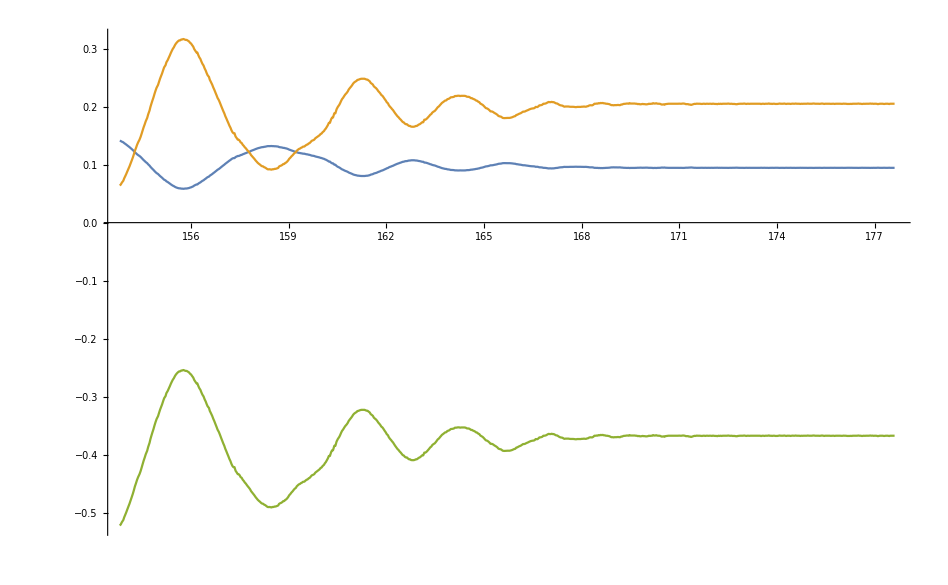

```mathematica
ListLinePlot[Transpose@{data[[All,1]],#}&/@Transpose[data][[2;;All]]]
```

# Process all the files

```mathematica
filenames=FileNames["data/raw/*.tsv"]
```

{data/raw/death1.tsv,data/raw/death2.tsv,data/raw/death3.tsv,data/raw/rocking1.tsv,data/raw/stabilizing1.tsv,data/raw/stablestart1.tsv}

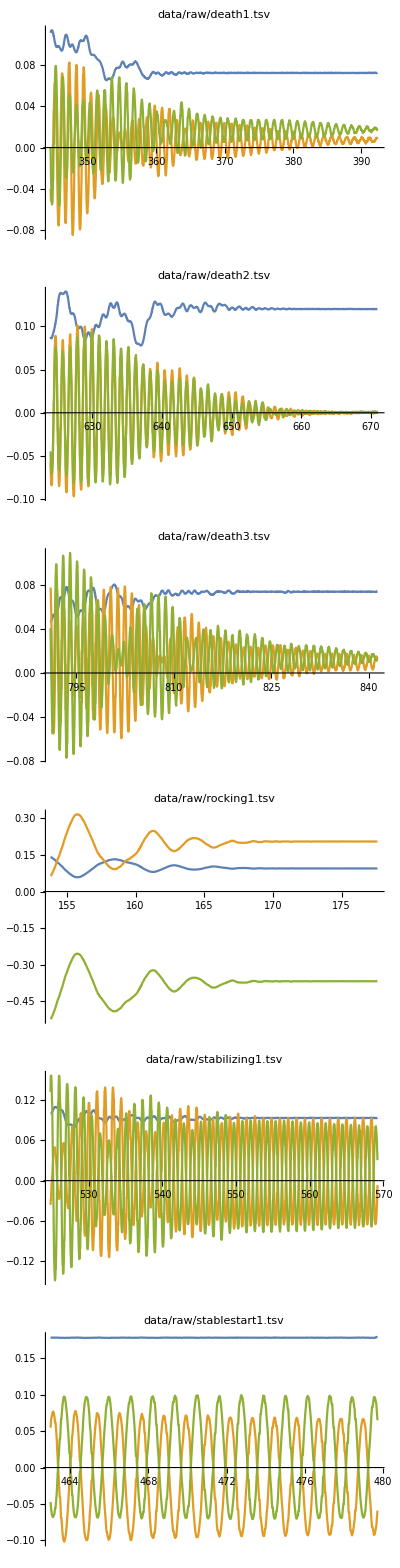

```mathematica
Column@Module[{data},
Table[data=preprocess[Import[f]];Export[StringReplace[f,"/raw/"->"/cleaned/"],data];
ListLinePlot[
Transpose@{data[[All,1]],#}&/@Transpose[data][[2;;All]],
PlotLabel->f,ImageSize->Large],
{f,filenames}]
]
```